1. Se escribe la ecuación en Mathematica

```mathematica
eqn = {x'[t]==a*(b-x[t]), x[0]==X0};
```

```mathematica
vars = {X0};
```

2. Se establecen los coeficientes a y b a 1 y se sustituyen en la ecuación.

```mathematica
pc = {a->1,b->1};
```

```mathematica
eq = eqn/.pc
```

{x'[t]==-x[t],x[0]==X0}

3. Se define Xo~U([0,1]

```mathematica
dvars = {UniformDistribution[{0,1}]};
```

4. Se generan las muestras de X0 tamaño con el número de iteraciones = 100 para el Método de MonteCarlo. (MMC)

```mathematica
niteraciones = 100;
```

```mathematica
muestra = Map[RandomVariate[#, niteraciones]&,dvars]//Transpose;
```

5. Se resuelve la EDO con los valores muestreados de Xo.

```mathematica
sol = ParallelMap[DSolve[eq/.Thread[vars->#],x[t], t]&,muestra];
```

```mathematica
sol = Map[x[t]/.#&, sol//Flatten];
```

6. Se dibujan todas las soluciones para t € [0, M], x[t]

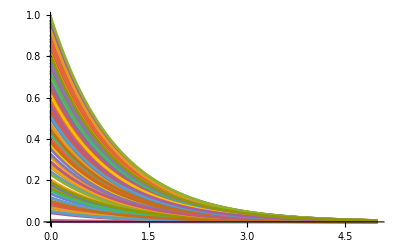

```mathematica
M = 5;
g =Plot[sol,{t,0,M},PlotRange->All, AxesOrigin->{0,0}]
```

7. Se calculan la media y la varianza del método de MC

```mathematica
mediaMC = Mean[sol]
varMC = Variance[sol]
```

0.480201 ⅇ^-t

0.080762 ⅇ^(-2 Re[t])

```mathematica
mediaMC/.{t->5}
varMC/.{t->5}
```

0.00323557

3.66659×10^-6